```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY182_cloudy/sec_int_data/862nm.dat"]
```

{{1.83648,-0.269214},{1.67469,-0.234875},{1.55096,-0.290031},{1.77833,-0.234988},{1.08395,-0.156221},{1.0884,1.21441},{1.10777,-0.303717},{1.1184,-0.21489},{1.90886,-0.281011}}

0.760911-0.579467 x

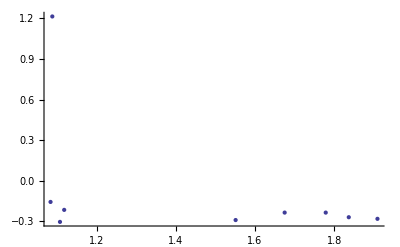

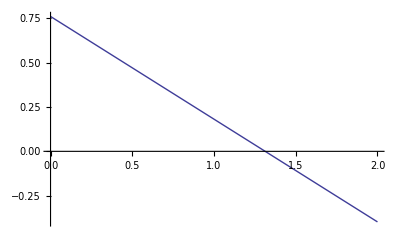

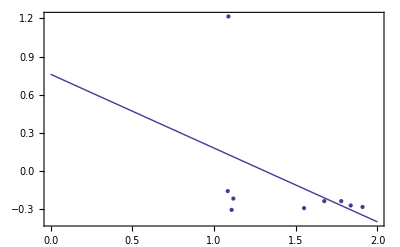

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```